# Kerr Quasi-Normal Modes

Quasi-normal modes of the Kerr geometry can be computed using the KerrQNM` package, building upon the common framework provided by the KerrModes` package.

## The Teukolsky radial equation

Building on the framework outlined in Modes of the Kerr Geometry, the KerrQNM` package make the following specific choices which cause the package to find quasi-normal modes:

ζ=ζ_+=+ⅈ ω, 
ξ=ξ_-=-s-ⅈ σ_+, 
η=η_+=-ⅈ σ_-.

With these choices, the recurrence relation coefficients α_n, β_n, and γ_n are uniquely determined.  The KerrQNM` package also provides the routine RadialCFRemainder which provides an estimate for r_N appropriate for computing quasi-normal modes.  Together, these provide the definitions necessary to compute the truncated continued fraction Cf(n,N).

Except for special cases where QNMs and TTMs coincide, quasi-normal modes cannot be determined by using a polynomial equation in place of the continued fraction, so the SelectMode function is not available within the KerrQNM` package.

## Supplying Initial Guesses

Finding any mode requires an initial guess for the mode frequency ω and the separation constant _s A_(ℓ,m)(c).  When a mode sequence does not already exist the ModeaStart option to KerrQNMSequence can be used to provide an initial guess at any value of the Kerr rotation parameter a.  Subsequent initial guesses for extending a sequence will be computed automatically from existing mode solutions.  On occasion, automatically generated guesses may fail.  In this case, the process of extending the sequence can be restarted and the ModeGuess option can be used to supply an alternative initial guess for the next value of a which will be attempted.

If the ModeaStart option is not used when creating a new sequence, then the new sequence will be started from the Schwarzschild limit a=0, and initial guesses will be taken from the global variable SchXXXTable.  The routine SchwarzschildQNM is provided to refine guesses already stored in  SchXXXTable.

Create a minimal table of Schwarzschild gravitational QNMs.

```mathematica
Needs["KerrQNM`"]
```

```mathematica
SetSpinWeight[-2]
```

All KerrMode routines (QNM) set for Spin-Weight s = -2

```mathematica
SchQNMTable[2,0]={0.374-0.089ⅈ,0};
SchQNMTable[2,1]={0.347-0.274ⅈ,1};
SchQNMTable[2,2]={0.301-0.478ⅈ,2};
SchQNMTable[2]=3;
SchQNMTable[3,0]={0.599-0.093ⅈ,0};
SchQNMTable[3,1]={0.583-0.281ⅈ,1};
SchQNMTable[3,2]={0.552-0.479ⅈ,2};
SchQNMTable[3]=3;
SchQNMTable[4,0]={0.809-0.094ⅈ,0};
SchQNMTable[4,1]={0.797-0.284ⅈ,1};
SchQNMTable[4,2]={0.773-0.480ⅈ,2};
SchQNMTable[3]=3;
```

```mathematica
For[l=2,l<=5,++l,
	For[n=0,n<=3,++n,SchwarzschildQNM[l,n];]
]
```

Computing (l=2,n=0)

{0.373671684418041835793492-0.0889623156889356982804609 ⅈ,0,300,-14,1.65399305838072362164263×10^-22}

```mathematica
⋮
```

Computing (l=5,n=3)

{0.955004006117707293908396-0.68055690864960645270547 ⅈ,3,300,-14,3.01999027664879868367663×10^-22}

Now create the ℓ=2, m=2, n=0 QNM sequence with an accuracy of 10^-5.

```mathematica
KerrQNMSequence[2,2,0,-5]
```

Set $MinPrecision = 24

Starting KerrQNM[2,2,0] sequence

ModeSol a=0. ω=0.373672-0.0889623 ⅈ Alm=4.

ModeSol a=0.001 ω=0.373798-0.0889603 ⅈ Alm=3.999+0.000237276 ⅈ

ModeSol a=0.002 ω=0.373924-0.0889583 ⅈ Alm=3.99801+0.00047464 ⅈ

ModeSol a=0.003 ω=0.37405-0.0889563 ⅈ Alm=3.99701+0.000712091 ⅈ

```mathematica
⋮
```

Decreasing Δa, blevel = 8

ModeSol a=0.99999609375 ω=0.997141-0.000696087 ⅈ Alm=0.55598+0.0029858 ⅈ

ModeSol+ a=0.999994140625 ω=0.9965-0.000851835 ⅈ Alm=0.558736+0.00365289 ⅈ

ModeSol- a=0.999990234375 ω=0.995485-0.00109826 ⅈ Alm=0.563103+0.00470766 ⅈ

Decreasing Δa, blevel = 9

ModeSol a=0.999998046875 ω=0.997977-0.000492786 ⅈ Alm=0.552384+0.00211449 ⅈ

ModeSol+ a=0.9999970703125 ω=0.997523-0.000603124 ⅈ Alm=0.554336+0.00258745 ⅈ

ModeSol- a=0.9999951171875 ω=0.996804-0.000777918 ⅈ Alm=0.557428+0.00333634 ⅈ

Decreasing Δa, blevel = 10

ModeSol a=0.9999990234375 ω=0.998569-0.000348755 ⅈ Alm=0.54984+0.00149683 ⅈ

Initial guesses can also be obtained from contour plots of the mode function.

Plot the real and imaginary zero contours of the mode function at a=1/10 with s=-2, m=3, and using the 2nd eigenvalue in the list of separation constants.

```mathematica
$MinPrecision=24;
```

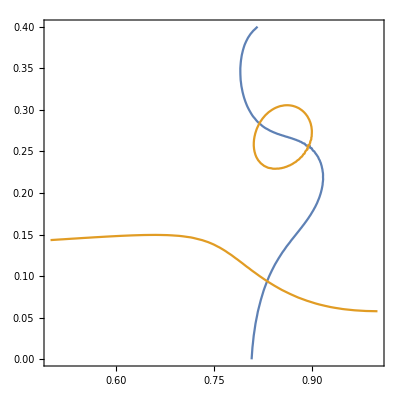

```mathematica
ContourPlot[{Re[PlotModeFunctionIndex[0,-2,3,1/10,2,ωr-ⅈ ωi,300,30]]==0,Im[PlotModeFunctionIndex[0,-2,3,1/10,2,ωr-ⅈ ωi,100,30]]==0},{ωr,0.5`24,1.0`24},{ωi,0.0`24,0.4`24}]
```

```mathematica
AngularSpectralRootIndex[-2,3,1/10(0.83-0.09ⅈ),2,30][[1]]
```

17.898+0.0113365 ⅈ

Use ω=0.83-0.09 ⅈ and _-2 A_(4,3)=17.9+0.113 ⅈ as an initial guess at a=1/10 and solve for the sequence in the backward direction.

```mathematica
KerrQNMSequence[4,3,0,-5,ModeaStart->{1/10,0.83-0.09ⅈ,17.9+0.0113ⅈ},SeqDirection->Backward]
```

Starting KerrQNM[4,3,0] sequence

ModeSol a=0.1 ω=0.831271-0.0939853 ⅈ Alm=17.8978+0.0118394 ⅈ

ModeSol a=0.099 ω=0.831038-0.0939879 ⅈ Alm=17.8989+0.0117156 ⅈ

ModeSol a=0.098 ω=0.830805-0.0939905 ⅈ Alm=17.8999+0.0115919 ⅈ

ModeSol a=0.097 ω=0.830573-0.0939931 ⅈ Alm=17.901+0.0114684 ⅈ

```mathematica
⋮
```

ModeSol a=0.003 ω=0.809808-0.0941608 ⅈ Alm=17.9971+0.000339473 ⅈ

ModeSol a=0.002 ω=0.809598-0.0941619 ⅈ Alm=17.9981+0.000226208 ⅈ

ModeSol a=0.001 ω=0.809388-0.0941629 ⅈ Alm=17.999+0.00011305 ⅈ

ModeSol a=0. ω=0.809178-0.094164 ⅈ Alm=18.

Related Guides

Kerr Quasi-Normal Modes

Modes of Kerr

Related Tech Notes

Modes of the Kerr Geometry

## Metadata

### Categorization

Tech Note

KerrQNM

KerrQNM`

KerrQNM/tutorial/KerrQuasi-NormalModes

### Keywords

Kerr

QNM

Quasinormal